```mathematica
T[n_,x_]:=(x^(5/3)*(1+f*n+g*n*(1-2x)) + (1-x)^(5/3)*(1+f*n-g*n*(1-2x)) )*2^(2/3)C*n^(5/3)
```

```mathematica
U[n_,x_]:=(a+4*b x (1-x))*n^2+(c+4 d x (1-x))n^(1+delta)
```

```mathematica
ST[n_,x_]:=Simplify[D[T[n,x],{x,2}]/(8 n)];SU[n_,x_]:=Simplify[D[U[n,x],{x,2}]/(8 n)]
```

```mathematica
ST[n_,x_]:=Simplify[(T[n,1/2]-T[n,0])/n];
SU[n_,x_]:=Simplify[(U[n,1/2]-U[n,0])/n];
```

```mathematica
Simplify[T[n,x]]
```

2^(2/3) C n^(5/3) ((1-x)^(5/3) (1+f n+g n (-1+2 x))+x^(5/3) (1+f n+g (n-2 n x)))

```mathematica
Solve[2^(2/3) C n^(5/3) ((1-x)^(5/3) (1+f n+g n (-1+2 x))+x^(5/3) (1+f n+g (n-2 n x)))==0,x]
```

$Aborted

```mathematica
Simplify[n^2*D[T[n,x]/n,n]]
```

1/3 2^(2/3) C n^(5/3) (2 (1-x)^(5/3)+5 f n (1-x)^(5/3)-5 g n (1-x)^(5/3)+10 g n (1-x)^(5/3) x+2 x^(5/3)+5 f n x^(5/3)+5 g n x^(5/3)-10 g n x^(8/3))

```mathematica
K=Simplify[9*D[Simplify[n^2*D[T[n,x]/n,n]],n]//.x->1/2]+Simplify[9*D[Simplify[n^2*D[U[n,x]/n,n]],n]//.x->1/2]
```

10 C n^(2/3) (1+4 f n)+9 (2 a n+2 b n+(c+d) delta (1+delta) n^delta)

```mathematica
BE=Simplify[(T[n,1/2]+U[n,1/2])/n]
```

a n+b n+c n^delta+d n^delta+C n^(2/3) (1+f n)

```mathematica
Simplify[n^2*D[U[n,x]/n,n]]
```

n (a n+c delta n^delta-4 (b n+d delta n^delta) (-1+x) x)

```mathematica
Sv=Simplify[(ST[n,x]+SU[n,x])//.x->1/2];
L=Simplify[3*n D[(ST[n,x]+SU[n,x]),n]//.x->1/2];
SK=Simplify[3*n ^2D[(ST[n,x]+SU[n,x]),{n,2}]//.x->1/2];
```

```mathematica
SK
```

6. n^(2/3) (d n^(4/3)+C (0.0652668+(-20.7666-0.326334 f) n-0.120822 Δ))

```mathematica
Sv//.{d->0}
```

b n-(mn Δ)/2-1/2 C n^(2/3) (-2+2 2^(2/3)+2 (-1+2^(2/3)) f n-2 2^(2/3) g n+Δ-2 2^(2/3) Δ)

```mathematica
L//.{d->0}
```

n^(2/3) (3 b n^(1/3)+C (2-2 2^(2/3)-5 (-1+2^(2/3)) f n+5 2^(2/3) g n-Δ+2 2^(2/3) Δ))

```mathematica
L0=L//.{d->0,f->0,g->0,Δ->0}
```

((2-2 2^(2/3)) C+3 b n^(1/3)) n^(2/3)

```mathematica
S0=Sv//.{d->0,f->0,g->0,Δ->0}
```

-1/2 (-2+2 2^(2/3)) C n^(2/3)+b n

```mathematica
CoefficientList[L//.d->0,{f,g}][[1,1]]
```

2 C n^(2/3)-2 2^(2/3) C n^(2/3)+3 b n-C n^(2/3) Δ+2 2^(2/3) C n^(2/3) Δ

```mathematica
B={LL-CoefficientList[L//.d->0,{b,g}][[1,1]],SD-CoefficientList[Sv//.d->0,{b,g}][[1,1]]}
```

{LL-2 C n^(2/3)+2 2^(2/3) C n^(2/3)+5 (-1+2^(2/3)) C f n^(5/3)+C n^(2/3) Δ-2 2^(2/3) C n^(2/3) Δ,-C n^(2/3)+2^(2/3) C n^(2/3)+(-1+2^(2/3)) C f n^(5/3)+SD+(mn Δ)/2+1/2 C n^(2/3) Δ-2^(2/3) C n^(2/3) Δ}

```mathematica
A={{CoefficientList[L//.d->0,{b,g}][[2,1]],CoefficientList[L//.d->0,{b,g}][[1,2]]},{CoefficientList[Sv//.d->0,{b,g}][[2,1]],CoefficientList[Sv//.d->0,{b,g}][[1,2]]}}
```

{{3 n,5 2^(2/3) C n^(5/3)},{n,2^(2/3) C n^(5/3)}}

```mathematica
Simplify[FullSimplify[Inverse[A].B]//.{f->0,LL->L0,Δ->0,SD->S0}]
```

{b,0}

```mathematica
(Simplify[Inverse[A].B]//.{Δ->0,f->0})[[1]]
```

(-2 LL+3 (-2+2 2^(2/3)) C n^(2/3)+10 SD)/(4 n)

```mathematica
(Simplify[Inverse[A].B]//.{Δ->0,f->0})[[2]]
```

(2 LL+(2-2 2^(2/3)) C n^(2/3)-6 SD)/(4 2^(2/3) C n^(5/3))

```mathematica
bf[LL_,SD_,n_]:=(-2 LL+3 (-2+2 2^(2/3)) C n^(2/3)+10 SD)/(4 n);gf[LL_,SD_,n_]:=(2 LL+(2-2 2^(2/3)) C n^(2/3)-6 SD)/(4 2^(2/3) C n^(5/3))
```

```mathematica
C=12
```

Set::wrsym: Symbol C is Protected.

12

```mathematica
b=bf[60,32,0.15]//.{C->12};g=gf[60,32,0.15]//.{C->12};
```

```mathematica
b
```

353.233

```mathematica
(ST[0.15,1/2]+SU[0.15,1/2])//.{C->12,d->0, Δ->0,f->0}
```

32.

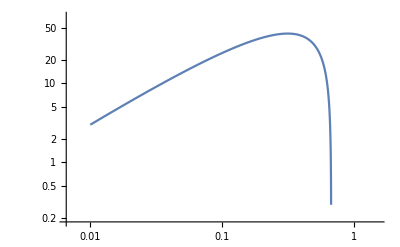

```mathematica
LogLogPlot[(ST[n,1/2]+SU[n,1/2])//.{C->12,d->0, Δ->0,f->0},{n,0.01,1.0}]
```

```mathematica
Simplify[D[nn*np*(nn+np)^(delta-1),np]]
```

nn (nn+np)^(-2+delta) (nn+delta np)

```mathematica
Simplify[D[(nn+np)^(delta),np]]
```

delta (nn+np)^(-1+delta)